```mathematica
(*p个q面骰子取最大的k个值*)
p=3;q=6;k=2;
all=Tuples[Range[1,q],k];
sta=Tally[Map[Total,Map[TakeLargest[k],all]]];
fst=First/@sta;
snd=Last/@sta;
```

```mathematica
Last/@sta
```

{1,2,3,4,5,6,5,4,3,2,1}

```mathematica
sta=Tally[Map[Total,Map[TakeLargest[k],all]]]
```

{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,5},{9,4},{10,3},{11,2},{12,1}}

```mathematica
fst=First/@sta
```

{2,3,4,5,6,7,8,9,10,11,12}

```mathematica
snd=Last/@sta
```

{1,2,3,4,5,6,5,4,3,2,1}

```mathematica
muf=Sum[i*x^j,{j,fst},{i,snd}]
```

36 x^2+36 x^3+36 x^4+36 x^5+36 x^6+36 x^7+36 x^8+36 x^9+36 x^10+36 x^11+36 x^12

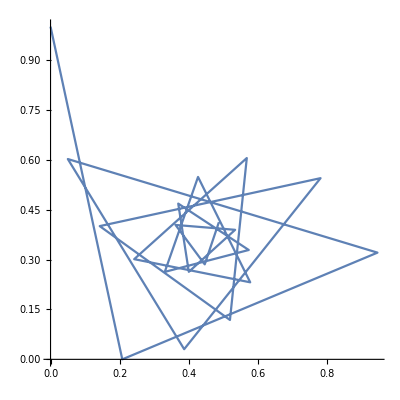

```mathematica
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@N[RecurrenceTable[{a[n+1]==I^a[n],a[0]==1},a, {n,1,20}]],AspectRatio->1]
```

```mathematica
ArrayPlot[CellularAutomaton[9,{{1},0},50]]
```

-Graphics-

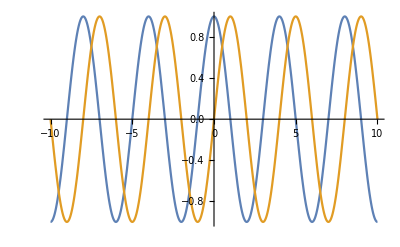

```mathematica
Plot[{Re[I^x],Im[I^x]},{x,-10,10}]
```

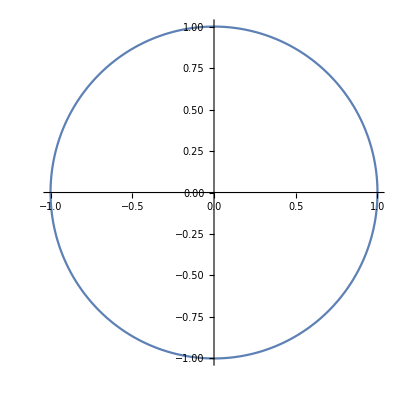

```mathematica
ParametricPlot[{Re[I^x],Im[I^x]},{x,-2,2}]
```